## Question 3

```mathematica
Clear["Global`*"]
```

```mathematica
polar[θ_]:=N[Mod[θ,2 Pi]] /; Mod[θ,2Pi]<=Pi
polar[θ_]:=N[(Mod[θ,2 Pi]-2 Pi) ]/; Mod[θ,2Pi]>Pi
```

```mathematica
b=2.5; f =.8; a =.01;
```

```mathematica
sol1 = NDSolve[{ω'[t] == -Sin[θ[t]] - a ω[t]+f Cos[b t], θ'[t] == ω[t], θ[0]==0,ω[0]==0},{θ,ω},{t,0,100}];
```

```mathematica
th[y_]:=Evaluate[θ[y]/.sol1][[1]]
```

```mathematica
o[y_]:=Evaluate[ω[y]/.sol1][[1]]
```

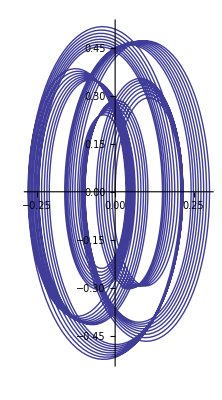

```mathematica
ParametricPlot[{θ[t],ω[t]}/.sol1,{t,0,100}]
```

```mathematica
Tt :=Table[polar[i],{i,0,100}];
p[i_]:= o[Tt[[i]]]
```

-803.258

```mathematica
q[i_]:=th[Tt[[i]]]
```

```mathematica
ParametricPlot[{q[i],p[i]},{i,0,100}]
```

Part::pspec: Part specification 0.00204082 is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 2.04286 is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.53096} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
poincare[b_,f_,a_,ndrop_,nplot_,psize_,pltr_]:=(T=2 π/b;g[{θold_,ωold_}]:={θ[T],ω[T]}/.NDSolve[{ω'[t] == -Sin[θ[t]] - a ω[t]+f Cos[b t], θ'[t] == ω[t], θ[0]==θold,ω[0]==ωold},{θ,ω},{t,0,T}][[1]];
lp=ListPlot[Drop[NestList[g,{polar[0],polar[0]},nplot+ndrop],ndrop],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","ω"}])
```

```mathematica
p1 =poincare[.3,.52,.2,500,5000,.02,.4];
```

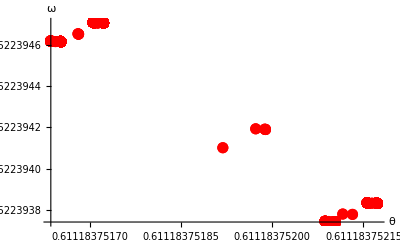

```mathematica
Show[p1,PlotRange->All]
```

This shows a more period pattern when the driving frequency is smaller

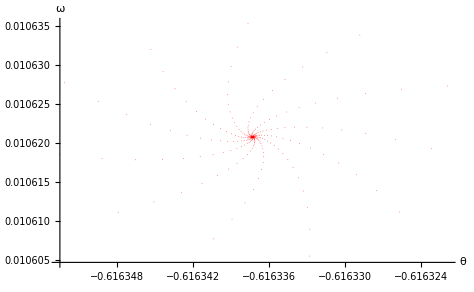

```mathematica
poincare[1.5,.8,.01,500,1000,.0002,.01]
```

And a more chaotic system when the driving frequency is high